```mathematica
Manipulate[
Module[{R,Pc,Tc,κ,A,B,a2,a1,a0,f,q,p,r,zmin,zmax,z,Z,f1,f2},
R=8.314;
Pc=22.12;Tc=647.3;

κ:=0.37464+1.54226*(0.344)-0.26992*(0.344)^2;

A[T_,P_]:=0.4572355289*(1+κ*(1-√(T/Tc)))^2*(Tc/T)^2*P/Pc;
B[T_,P_]:=0.0777960739*Tc/T*P/Pc;

a2[T_,P_]:=B[T,P]-1;
a1[T_,P_]:=A[T,P]-3*B[T,P]^2-2*B[T,P];
a0[T_,P_]:=-(A[T,P]*B[T,P]-B[T,P]^2-B[T,P]^3);

f[T_,P_,z_]:=P*Exp[z[T,P]-1-Log[z[T,P]-B[T,P]]-A[T,P]/(2.8284*B[T,P])*Log[(z[T,P]+2.4142*B[T,P])/(z[T,P]-0.4142*B[T,P])]];

q[T_,P_]:=(2*a2[T,P]^3-9*a2[T,P]*a1[T,P]+27*a0[T,P])/27;
p[T_,P_]:=(3*a1[T,P]-a2[T,P]^2)/3;
r[T_,P_]:=q[T,P]^2/4+p[T,P]^3/27;

zmin[T_,P_]:=2*√(-p[T,P]/3)*Cos[ArcCos[(3*q[T,P])/(p[T,P]*2*√(-p[T,P]/3))]/3+2*π/3]-a2[T,P]/3;
zmax[T_,P_]:=2*√(-p[T,P]/3)*Cos[ArcCos[(3*q[T,P])/(p[T,P]*2*√(-p[T,P]/3))]/3]-a2[T,P]/3;

z[T_,P_]:=Piecewise[{
{CubeRoot[-q[T,P]/2+√r[T,P]]+CubeRoot[-q[T,P]/2-√r[T,P]]-a2[T,P]/3,r[T,P]>0},
{If[f[T,P,zmin]<f[T,P,zmax],zmin[T,P],zmax[T,P]],r[T,P]≤0}
}];

Table[Z[P_,t_]:=Interpolation[Table[{T,z[T,P]},{T,200,750,5}]]@x/.x->t,{P,1.5,50,0.1}];

Z[2,200]
],
Control[{{P2,5.1,"P_2"},1.5,50,0.1,Appearance->"Labeled"}]
]
```

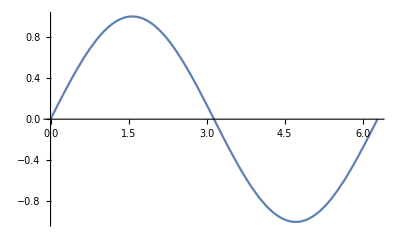

```mathematica
Module[{y,f},
y[x_,a_]:=a*Sin[x];
Table[f[a_]=Interpolation[Table[{x,y[x,a]},{x,0,2*π,0.1}]]@z,{a,1,3}];
Plot[f[1],{z,0,2*π}]
]
```

```mathematica
(*Table[(*Subscript[z, P]=Interpolation@*)Table[{T,Z[T,P]},{T,300,400,10}],{P,5,50,5}]*)

(*Plot[Through@Table[Interpolation@Table[{T,Z[T,P]},{T,300,400,10}],{P,1,3}]@temp,{temp,300,400}]*)
```

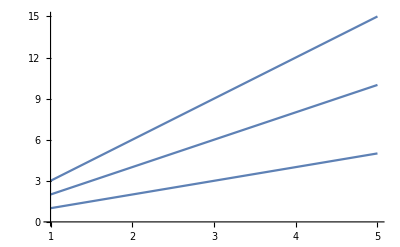

```mathematica
Module[{f},
f=Table[Interpolation@Table[{i,j*i},{i,1,5}],{j,1,3}];
Plot[Through@f@x,{x,1,5}];
Plot[Through@Table[Interpolation@Table[{i,j*i},{i,1,5}],{j,1,3}]@x,{x,1,5}]
]
```